```mathematica
SetDirectory[NotebookDirectory[]];
data=Partition[Delete[ReadList["data/outMexplicitEuler.txt", Real], 1], 2];
```

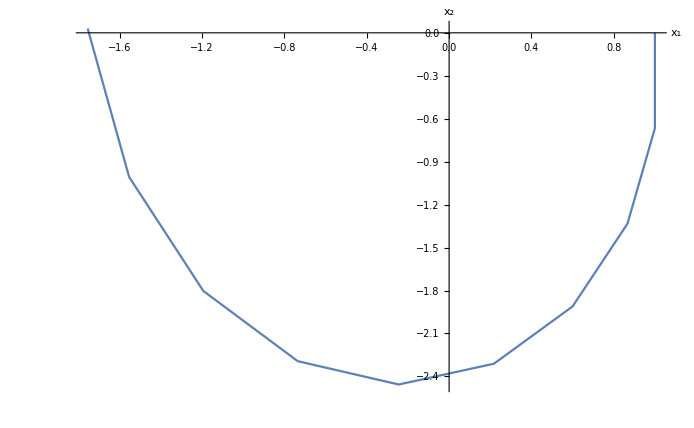

```mathematica
Show[ListLinePlot[{data},AxesLabel->{"x_1","x_2"},AxesStyle->Thick,LabelStyle->Directive[20]]]
```